```mathematica
k1wfc1=Import["/Users/Nevensky/Desktop/projBands/test/k1wfc1.dat"];
k1wfc1=k1wfc1[[All,1]]+I *k1wfc1[[All,2]];
```

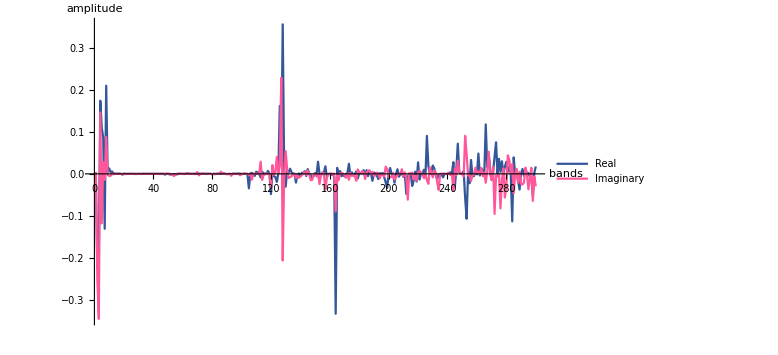

```mathematica
ListLinePlot[{Re[k1wfc1],Im[k1wfc1]},PlotRange->Full,AxesLabel->{"bands","amplitude"},PlotLegends->{"Real","Imaginary"},ImageSize->Large,PlotStyle->{RGBColor[0.2, 0.34, 0.6],RGBColor[1, 0.34, 0.6]}]
```

```mathematica
k1rho1=Abs[k1wfc1]^2;
```

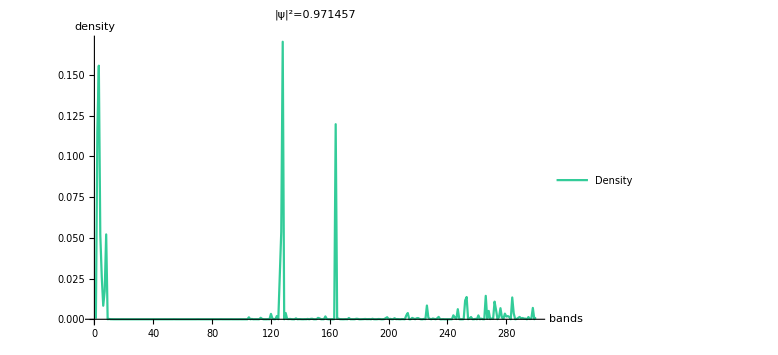

```mathematica
ListLinePlot[k1rho1,PlotRange->Full,AxesLabel->{"bands","density"},PlotLegends->{"Density"},ImageSize->Large,PlotStyle->RGBColor[0.2, 0.8, 0.6],PlotLabel->StringJoin["|ψ|^2=",ToString[Total[k1rho1]]]]
```